# Inlämningsuppgift 1

## Uppgift 1

### Hitta lösningarna till polynomekvationen: 2/3 x^5-2/3 x^4-8 x^3+8 x^2+18x-18=0. Rita också grafen för polynomet och markera nollställen med en röd punkt.

Jag gör en funktion av polynomet.

```mathematica
f[x_]=((2/3)x^5)-((2/3)x^4)-(8x^3)+(8x^2)+18x-18
```

-18+18 x+8 x^2-8 x^3-(2 x^4)/3+(2 x^5)/3

Vi vet att det kommer att finnas fem lösningar i ekvationen. Vi behöver därför fem variabler där vi sparar lösningarna från ekvationen som vi får fram genom Solve.

```mathematica
{x1,x2,x3,x4,x5}=x/.Solve[f[x]==0,x]
```

{-3,1,3,-√3,√3}

Lösningarna är:  -3,1,3,-√3,√3. Dessa är sparade i x1,x2,x3,x4,x5.

Nedan ritar vi upp en graf för polynomet och markerar dess nollställen med röd punkt.

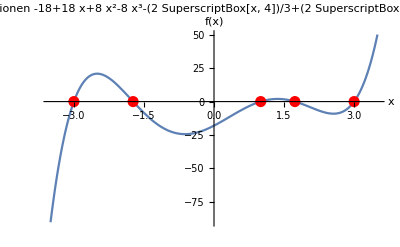

```mathematica
Plot[f[x],{x,-3.5,3.5},AxesLabel->{"x","f(x)"},PlotLabel->"Ekvationen -18+18 x+8 x^2-8 x^3-(2 SuperscriptBox[x, 4])/3+(2 SuperscriptBox[x, 5])/3=0",Epilog->{PointSize[0.02],Red,Point[{{x1,f[x1]},{x2,f[x2]},{x3,f[x3]},{x4,f[x4]},{x5,f[x5]}}]}]
```

Problemet är nu löst. Vi har ritat upp grafen för polynomet i ett lämpligt intervall där nollställena finns markerade. Problemet löstes genom att använda mathematicas Solve-funktion för att ta reda på lösningarna samt Plot-funktionen för att rita upp själva grafen.

## Uppgift 2

### Lös ekvationen |x-1|+|x-3|=4. Illustrera lösningsområdet grafiskt.

Abs[-3+x]+Abs[-1+x]

```mathematica
f[x_]=Abs[x-1]+Abs[x-3]
```

Abs[-3+x]+Abs[-1+x]

```mathematica
Reduce[Abs[x-1]+Abs[x-3]==4,x,Reals]
```

x==0||x==4

Lösningarna till ekvationen är x=0 eller x=4. Vi ritar upp ekvationen |x-1|+|x-3| samt lösningen y=4. Vi ser då också grafiskt vad lösningarna blir.

```mathematica
x1=0;
x2=4;
```

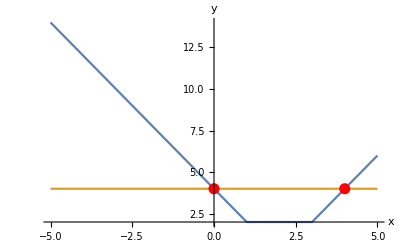

```mathematica
Plot[{f[x],4},{x,-5,5},AxesLabel->{"x","y"},Epilog->{PointSize[0.02],Red,Point[{{x1,f[x1]},{x2,f[x2]}}]}]
```

Problemet är nu löst. Vi har ritat upp ekvationen |x-1|+|x-3| samt lösningen y=4. Vi ser grafiskt att det finns två lösningar.

## Uppgift 3

### Finn lösningen till ekvationen z^7=2-i och visa grafiskt att dessa ligger på en cirkel i komplexa talplanet.

Vi vet att ekvationen kan skrivas om till polär form, z^n=r^n(Cos(nv)+iSin(nv)), där n är 7 i vår ekvation. Vi vet även att r är avståndet till punkten i det imaginära planet från origo. Detta ger att r=√(a^2+b^2). Vi vet också att ekvationen kan skrivas som z=a+b i. Vi vet också att argumentet av z, eller arg z=tan^-1(b/a) då a>0. Detta skriver jag också som v högre upp i denna text.

Vi kan nu alltså skriva om z^7=2-i som följande på polär form:
r^7(Cos(7v)+i Sin(7v))=√(2^2+1^2)(Cos(Tan^-1(-1/2))+i Sin(Tan^-1(-1/2))).
Detta betyder att:
r=5^(1/14), v=((Tan^-1(-1/2))/7)+k 2π/7 . Där k=0,1,2,3,4,5,6.
Nedan för jag in de olika lösningarna i variablerna z0,z1,z2,z3,z4,z5,z6.

```mathematica
r=((5^(1/2))^(1/7))
```

5^(1/14)

```mathematica
z0=r*(Cos[ArcTan[-1/2]/7]+I*Sin[ArcTan[-1/2]/7])
```

5^(1/14) (Cos[1/7 ArcTan[1/2]]-ⅈ Sin[1/7 ArcTan[1/2]])

```mathematica
z1=r*(Cos[(ArcTan[-1/2]/7)+((2*Pi)/7)]+(I*Sin[(ArcTan[-1/2]/7)+((2*Pi)/7)]))
```

5^(1/14) (ⅈ Cos[(3 π)/14+1/7 ArcTan[1/2]]+Sin[(3 π)/14+1/7 ArcTan[1/2]])

```mathematica
z2=r*(Cos[(ArcTan[-1/2]/7)+((4*Pi)/7)]+(I*Sin[(ArcTan[-1/2]/7)+((4*Pi)/7)]))
```

5^(1/14) (ⅈ Cos[π/14-1/7 ArcTan[1/2]]-Sin[π/14-1/7 ArcTan[1/2]])

```mathematica
z3=r*(Cos[(ArcTan[-1/2]/7)+((6*Pi)/7)]+(I*Sin[(ArcTan[-1/2]/7)+((6*Pi)/7)]))
```

5^(1/14) (-Cos[π/7+1/7 ArcTan[1/2]]+ⅈ Sin[π/7+1/7 ArcTan[1/2]])

```mathematica
z4=r*(Cos[(ArcTan[-1/2]/7)+((8*Pi)/7)]+(I*Sin[(ArcTan[-1/2]/7)+((8*Pi)/7)]))
```

5^(1/14) (-Cos[π/7-1/7 ArcTan[1/2]]-ⅈ Sin[π/7-1/7 ArcTan[1/2]])

```mathematica
z5=r*(Cos[(ArcTan[-1/2]/7)+((10*Pi)/7)]+(I*Sin[(ArcTan[-1/2]/7)+((10*Pi)/7)]))
```

5^(1/14) (-ⅈ Cos[π/14+1/7 ArcTan[1/2]]-Sin[π/14+1/7 ArcTan[1/2]])

```mathematica
z6=r*(Cos[(ArcTan[-1/2]/7)+((12*Pi)/7)]+(I*Sin[(ArcTan[-1/2]/7)+((12*Pi)/7)]))
```

5^(1/14) (-ⅈ Cos[(3 π)/14-1/7 ArcTan[1/2]]+Sin[(3 π)/14-1/7 ArcTan[1/2]])

När jag nu fört in alla lösningar, lägger jag in de i en lista, sol.

```mathematica
sol={z0,z1,z2,z3,z4,z5,z6};
```

Nu delar jag upp listan i en ny lista med reella delen samt den imaginära delen för sig.

```mathematica
pp=Table[{Re[sol[[i]]],Im[sol[[i]]]},{i,1,7}];
```

Nedan skriver jag ut punkterna på det komplexa talplanet samt visar att en cirkel med mittpunkt i origo och radien r=5^(1/14), samma r som vi räknat ut ovan går igenom samtliga lösningar. D.v.s. lösningarna ligger på en cirkel i det komplexa talplanet.

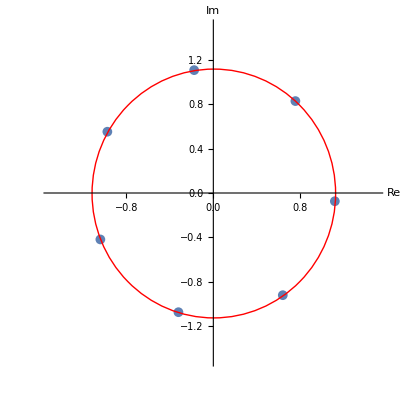

```mathematica
ListPlot[pp,AxesLabel->{"Re","Im"},AspectRatio->Automatic, PlotMarkers->{Automatic,Medium},Epilog->{Red,Circle[{0,0},(5^(1/14))]},PlotRange->{{-1.5,1.5},{-1.5,1.5}}]
```

## Uppgift 4

### En paradox är ett påstående som förefaller korrekt utifrån sanna antaganden men leder till självmotsägelser eller till logiskt oacceptabla slutsatser [Wikipedia]. Akilles och sköldpaddan är en av Zenons paradoxer. Antag att Akilles springer 10 gånger så fort som sköldpaddan. De båda skall tävla vem som först kommer i mål på 100 meter. Då sköldpaddan är långsammare än Akilles så får den ett försprång på 80 meter. Paradoxen är att när Akilles har sprungit dessa 80 meter, så har sköldpaddan kommit 8 meter, när Akilles har sprungit dessa 8 meter har sköldpaddan kommit 8 dm. Det resonemanget skulle leda till att Akilles aldrig kommer i kapp sköldpaddan. Undersök och förklara paradoxen genom att rita tid-sträcka grafer för Akilles och Sköldpaddan. Dessutom beskriv en formel för talföljden ovan och beräkna serien för den med hjälp av Mathematica. När kommer Akilles i kapp sköldpaddan? Visa paradoxen både numeriskt och grafiskt.

Det är endast en paradox om man baserar Akilles nuvarande hastighet på sköldpaddans nuvarande hastighet. En mer rimlig beskrivning vore att Akilles är tio gången snabbare än sköldpaddan i början och att detta håller i sig.
Vi börjar vår tid från det att sköldpaddan har sprungit 80m. Då blir funktionen för sköldpaddan f(x)=x/10+80. För Akilles blir det f(x)=x. Då sköldpaddan är tio gånger långsammare än Akilles får vi dela sköldpaddans förändringsfaktor med tio.

```mathematica
f[x_]=x/10+80
```

80+x/10

```mathematica
s[x_]=x
```

x

```mathematica
Solve[x==(x/10)+80,x]
```

{{x→800/9}}

```mathematica
N[800/9]
```

88.8889

Som vi ser här kommer Akilles att ha kommit ikapp sköldpaddan då x=800/9. Det numeriska värdet blir 88.8889.

```mathematica
Plot[{f[x],s[x]},{x,0,100},AxesLabel->{"Tid","Sträcka"},PlotLabels->{"Sköldpaddan","Akilles"},Epilog->{PointSize[0.03],Red,Point[{800/9,800/9}]},PlotLabel->"Verkligheten"]
```

-Graphics-

Formeln för paradoxen och talföljden blir då ∑_(n=0)^∞ 80/10^n.
Vi beräknar den summan nedan och får svaret 800/9. Om vi tolkar uppgiften som en paradox så kommer ingen av tävlanden att komma 100m. Sträckan kommer att gå mot 800/9 då tiden blir oändligt stor.

```mathematica
Sum[80/(10^n),{n,0,Infinity}]
```

800/9

Nedan skriver vi in punkter i listor. pointsA för Akilles tider och sträckor. pointsS för sköldpaddans tider och sträckor. Jag begränsar mig till sex stycken tidsenheter då vi ändå inte kommer kunna urskilja något bortom det. Sträckan får vi genom att ange respektive n-värde i summafunktionen. Fast här under använder jag x istället för n.

```mathematica
pointsA={{0,0},{1,Sum[80/10^x,{x,0,0}]},{2,Sum[80/10^x,{x,0,1}]},{3,Sum[80/10^x,{x,0,2}]},{4,Sum[80/10^x,{x,0,3}]},{5,Sum[80/10^x,{x,0,4}]}}
```

{{0,0},{1,80},{2,88},{3,444/5},{4,2222/25},{5,11111/125}}

```mathematica
pointsS={{0,80},{1,Sum[80/10^x,{x,0,1}]},{2,Sum[80/10^x,{x,0,2}]},{3,Sum[80/10^x,{x,0,3}]},{4,Sum[80/10^x,{x,0,4}]},{5,Sum[80/10^x,{x,0,5}]}}
```

{{0,80},{1,88},{2,444/5},{3,2222/25},{4,11111/125},{5,111111/1250}}

```mathematica
ListPlot[{pointsA,pointsS},PlotRange->{{0,6},{0,100}},Joined->True,AxesLabel->{"Tid","Sträcka"},PlotLabels->{"Akilles","Sköldpaddan"},PlotLabel->"Paradoxen"]
```

-Graphics-